# a-Y Phase Spaces and Potentials

## Define Variables and Parameters

```mathematica
(*Clear all variables*)
ClearAll["Global`*"];
```

```mathematica
(*Dark matter (z), radiation (v) and dark energy x written in terms of the scale factor a*)
ca[x0_]=(1-x0)/(x0-R);

x[a_,x0_]=(a^(-3*(1-R))+ca[x0]*R)/(a^(-3*(1-R))+ca[x0]);

z[a_,x0_,c_]=c*((x[a,x0]-R)/(1-x[a,x0]))^(1/(1-R));

v[a_,x0_,cv_]=cv*((x[a,x0]-R)/(1-x[a,x0]))^(4/(3*(1-R)));
```

```mathematica
(*Define R and cv*)
R=0.05;
cv=0.000034;
```

```mathematica
(*Define w, the resulting term left in y' when y = 0, which needs to be solved to find the Einstein fixed points*)
(*When w = 0, there is an Einstein fixed point*)
w[a_,x0_,c_,cv_]=z[a,x0,c]+2*v[a,x0,cv]-3*R+x[a,x0]*(1+3*R)-3*x[a,x0]^2;
```

```mathematica
(*Import values of c*)
c=Flatten[Import["G:\\My Drive\\Wolfram Mathematica\\Project 1\\Non_Interacting_Matter\\Compact_Variables\\Full_Case\\x_Y_Z_R0.05\\cValues.csv"]]
```

{0.05,0.200851,0.25,0.319517,0.35,0.386125,0.5}

## Find the Einstein Points in Each Case

```mathematica
(*Numerically solve w = 0 to find the Einstein fixed points in each case*)
(*FindRoot is a Newtonian approximation*)
```

### One Einstein Point: c1

```mathematica
aOneEinsteinPointc1=FindRoot[w[a,0.2,c[[1]],cv]==0,{a,0.2}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc1=a/.aOneEinsteinPointc1
```

0.1668

### Two Einstein Points: c2 (1st Limiting Case)

```mathematica
aTwoEinsteinPointsc2i=FindRoot[w[a,0.1,c[[2]],cv]==0,{a,0.1}];
aTwoEinsteinPointsc2ii=FindRoot[w[a,0.1,c[[2]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc2={a/.aTwoEinsteinPointsc2i,a/.aTwoEinsteinPointsc2ii}
```

{0.188558,0.581076}

### Three Einstein Points: c3

```mathematica
aThreeEinsteinPointsc3i=FindRoot[w[a,0.08,c[[3]],cv]==0,{a,0.1}];
aThreeEinsteinPointsc3ii=FindRoot[w[a,0.08,c[[3]],cv]==0,{a,0.4}];
aThreeEinsteinPointsc3iii=FindRoot[w[a,0.08,c[[3]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc3={a/.aThreeEinsteinPointsc3i,a/.aThreeEinsteinPointsc3ii,a/.aThreeEinsteinPointsc3iii}
```

{0.174822,0.402707,0.555175}

### Three Einstein Points: c4

```mathematica
aThreeEinsteinPointsc4i=FindRoot[w[a,0.08,c[[4]],cv]==0,{a,0.1}];
aThreeEinsteinPointsc4ii=FindRoot[w[a,0.08,c[[4]],cv]==0,{a,0.4}];
aThreeEinsteinPointsc4iii=FindRoot[w[a,0.08,c[[4]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc4={a/.aThreeEinsteinPointsc4i,a/.aThreeEinsteinPointsc4ii,a/.aThreeEinsteinPointsc4iii}
```

{0.204402,0.348764,0.348764}

### Three Einstein Points: c5

```mathematica
aThreeEinsteinPointsc5i=FindRoot[w[a,0.08,c[[5]],cv]==0,{a,0.1}];
aThreeEinsteinPointsc5ii=FindRoot[w[a,0.08,c[[5]],cv]==0,{a,0.4}];
aThreeEinsteinPointsc5iii=FindRoot[w[a,0.08,c[[5]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aThreeEinsteinPointsc5={a/.aThreeEinsteinPointsc5i,a/.aThreeEinsteinPointsc5ii,a/.aThreeEinsteinPointsc5iii}
```

{0.221488,0.324423,0.324423}

### Two Einstein Points: c6 (2nd Limiting Case)

```mathematica
aTwoEinsteinPointsc6i=FindRoot[w[a,0.9,c[[6]],cv]==0,{a,0.1}];
aTwoEinsteinPointsc6ii=FindRoot[w[a,0.9,c[[6]],cv]==0,{a,0.9}];
```

```mathematica
(*Put the Einstein points into one variable name for this case*)
aTwoEinsteinPointsc6={a/.aTwoEinsteinPointsc6i,a/.aTwoEinsteinPointsc6ii}
```

{1.89688,1.89688}

### One Einstein Point: c7

```mathematica
aOneEinsteinPointc7=FindRoot[w[a,0.9,c[[7]],cv]==0,{a,0.1}];
```

```mathematica
(*Remove the arrow from the solution above*)
aOneEinsteinPointc7=a/.aOneEinsteinPointc7
```

4.64873

## Define Variables for Phase Spaces and Potentials

### Phase Spaces

```mathematica
(*Define the Flat Friedmann Separatrix (FFS)*)
(*Define ffs = y^2*)
ffs[a_,x0_]=(1/3)*(x[a,x0]+z[a,x0,c]+v[a,x0,cv]);
```

```mathematica
(*Rearrange for y*)
FFS[a_,x0_]=Sqrt[ffs[a,x0]];
```

```mathematica
(*Define the Closed Friedmann Separatrix (CFS)*)
(*Define cfs = y^2*)
(*aE denotes the a value of the Einstein fixed point*)
cfs[a_,aE_,x0_]= x[a,x0]/3+z[a,x0,c]/3+v[a,x0,cv]/3-((aE/a)^2)*(x[aE,x0]/3+z[aE,x0,c]/3+v[aE,x0,cv]/3);
```

```mathematica
(*Rearrange above equation for y*)
CFS[a_,aE_,x0_]=Sqrt[cfs[a,aE,x0]];
```

```mathematica
(*Define the acceleration*)
Accn=z[a,x0,c]+x+2*v[a,x0,cv]-3*R+3*R*x[a,x0]-3*x[a,x0]^2;
```

## One Einstein Point: c1

```mathematica
(*Trajectories for the phase space*)
(*Take a0 = 1*)
a0=1;

trajc1[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[1]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[1]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c1traj[1]=ContourPlot[Evaluate[trajc1[0,0.2]],{a,0,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[2]=ContourPlot[Evaluate[trajc1[0,0.2]],{a,0,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[3]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{a,0,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[4]=ContourPlot[Evaluate[trajc1[0.12,0.2]],{a,0,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[5]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{a,0,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[6]=ContourPlot[Evaluate[trajc1[0.18,0.2]],{a,0,3},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[7]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[8]=ContourPlot[Evaluate[trajc1[0.225,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[9]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[10]=ContourPlot[Evaluate[trajc1[0.5,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[11]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{a,0,3},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c1traj[12]=ContourPlot[Evaluate[trajc1[0.9,0.2]],{a,0,3},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc1=Table[c1traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc1=Plot[{FFS[a,0.2][[1]],-FFS[a,0.2][[1]]},{a,0,3},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc1=Plot[{CFS[a,aOneEinsteinPointc1,0.2][[1]],-CFS[a,aOneEinsteinPointc1,0.2][[1]]},{a,0,3},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc1=ListPlot[{{aOneEinsteinPointc1,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc1=ContourPlot[Accn[[1]]==0,{a,0,1},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

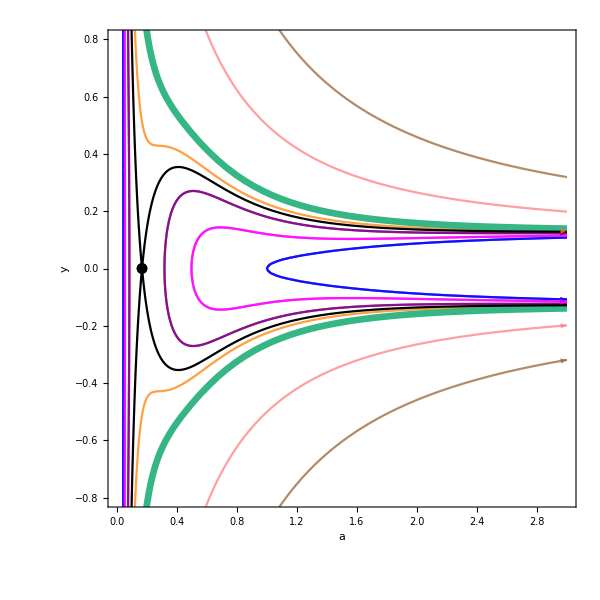

```mathematica
(*Show all components of plots*)
PhaseSpacec1=Show[Trajc1,FFSc1,CFSc1,Einsteinc1,PlotRange->{-0.8,0.8},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```

## One Einstein Point: c7

```mathematica
(*Trajectories for the phase space*)
trajc7[y0_,x0_]:=y^2==x[a,x0]/3+z[a,x0,c[[7]]]/3+v[a,x0,cv]/3-(1/a^2)*(x[a0,x0]/3+z[a0,x0,c[[7]]]/3+v[a0,x0,cv]/3-y0^2);
```

```mathematica
c7traj[1]=ContourPlot[Evaluate[trajc7[0,0.9]],{a,0,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[2]=ContourPlot[Evaluate[trajc7[0,0.9]],{a,0,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Blue, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[3]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{a,0,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[4]=ContourPlot[Evaluate[trajc7[0.5,0.9]],{a,0,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Magenta, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[5]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{a,0,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[6]=ContourPlot[Evaluate[trajc7[0.56,0.9]],{a,0,10},{y,-1.5,1.5},PlotPoints->100,ContourStyle -> {{Purple, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[7]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[8]=ContourPlot[Evaluate[trajc7[0.7,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Orange, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[9]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[10]=ContourPlot[Evaluate[trajc7[0.92,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Pink, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[11]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{a,0,10},{y,0,1.5},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,-.02,-.02,0},1]]],Arrow[x]};
```

```mathematica
c7traj[12]=ContourPlot[Evaluate[trajc7[0.99,0.9]],{a,0,10},{y,-1.5,0},PlotPoints->100,ContourStyle -> {{Brown, Opacity[0.75]}}]/. Line[x_]:>{Arrowheads[Flatten[Table[{0,.02,.02,0},1]]],Arrow[x]};
```

```mathematica
(*Add trajectories into a table*)
Trajc7=Table[c7traj[i],{i,1,12}];
```

```mathematica
(*Plot the FFS*)
(*Plot + and - FFS as a Sqrt was taken and Mathematica defaults to the + only*)
FFSc7=Plot[{FFS[a,0.9][[7]],-FFS[a,0.9][[7]]},{a,0,10},PlotStyle->{{RGBColor[0.21,0.71,0.52],Thickness[0.008]}},PlotRange->All];
```

```mathematica
(*Plot the CFS*)
(*Plot + and - CFS as a Sqrt was taken and Mathematica defaults to the + only*)
CFSc7=Plot[{CFS[a,aOneEinsteinPointc7,0.9][[7]],-CFS[a,aOneEinsteinPointc7,0.9][[7]]},{a,0,10},PlotStyle->{Black},PlotRange->All];
```

```mathematica
(*Plot the Einstein fixed points for this case*)
Einsteinc7=ListPlot[{{aOneEinsteinPointc7,0}},PlotStyle->{Black}];
```

```mathematica
(*Plot the accn = 0 curve for this case*)
Accnc7=ContourPlot[Accn[[7]]==0,{a,0,1},{y,-1.5,1.5},ContourStyle->{Red, Thick}];
```

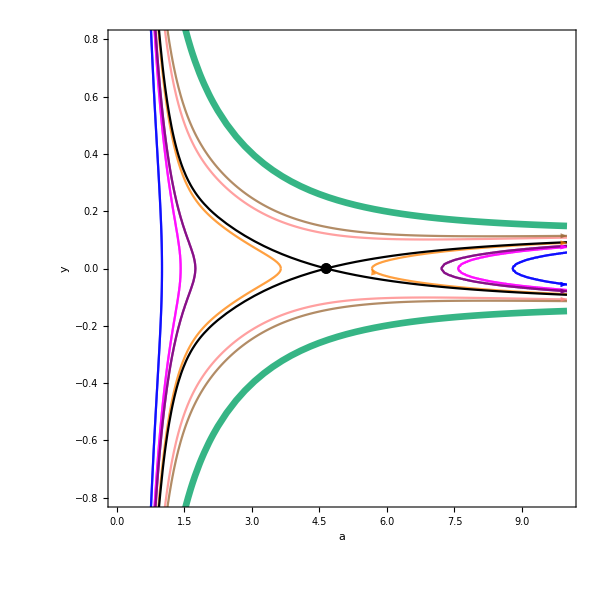

```mathematica
(*Show all components of plots*)
PhaseSpacec7=Show[Trajc7,FFSc7,CFSc7,Einsteinc7,PlotRange->{-0.8,0.8},FrameLabel->{"a",Rotate["y",270Degree]},AspectRatio->1,ImageSize->{600,600},BaseStyle->{FontSize->14}]
```